```mathematica
ClearAll
rau=0.2201
teta = 5.67318*(Pi/180)
alfa = 1 * Pi / 180
lambda = 0.619927*10^-7
k=2*Pi/lambda
h=2*k*Sin[teta]
chizero=-0.242370*10^-5+I*0.918640*10^-8
chih = (-0.922187+I*0.913110)*10^-6
chimh=I*chih
chih2=chih*chimh
u2=0.25*chih2*k^2
t = 0.250
p=29*10^3
rayon=2000
raygam = rayon * Cos[teta]
kp=k*Sin[2*teta]
kp2=kp*Sin[2*teta]
```

ClearAll

0.2201

0.0990157

π/180

6.19927×10^-8

1.01354×10^8

2.00384×10^7

-2.4237×10^-6+9.1864×10^-9 ⅈ

-9.22187×10^-7+9.1311×10^-7 ⅈ

-9.1311×10^-7-9.22187×10^-7 ⅈ

1.68412×10^-12+1.6659×10^-14 ⅈ

4325.05+42.7826 ⅈ

0.25

29000

2000

1990.2

1.99403×10^7

3.92304×10^6

```mathematica
sg=1
teta1=alfa+sg*teta
teta2=alfa-sg*teta
fam1=Sin[teta1]
fam2=Sin[teta2]
gam1=Cos[teta1]
gam2=Cos[teta2]
t1=t/gam1
t2=t/gam2
qpoly=p * rayon * gam2 / (2 * p + rayon * gam1)
att = Exp[-0.5*k*(t1+t2)* Im[chizero]];{"att",att}
s2max=0.25*t1*t2
u2max = u2 * s2max
gama=t2/t1
a=Sin[2*teta]*t1*0.5
kin=0.25*(t1-t2)*chizero/a
kinx=Re[kin]
kiny=Im[kin]
com=Sin[alfa]*(1+gam1*gam2*(1+rau))
kp3=0.5*k*(gama*a)^2
mu1=sg*(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta])
mu2=-sg * (Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta])
a1=sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta1]+ rau * Sin[alfa]Cos[teta1]) 
a2=-sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta2]+ rau * Sin[alfa]Cos[teta2])
acrist=-sg*h*com/rayon
acmax=acrist * s2max
g=gama * acrist * rayon/kp2
kap=u2max/acmax
pe=p*rayon/(gama^2*(rayon+p*mu2)-g*p)
qe[q_]:=q*rayon/(rayon-q*mu1-g * q);
be[q_]:=1/qe[q]+1/pe;
invle[q_]:=1/(pe+qe[q])+ g / rayon;
sgplus[x_,q_]:=NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k * v^2 *invle[q]-k*v*kiny]*Cos[k*v*x/(q * pe * be[q])], {v,-a,a}];
```

1

0.116469

-0.0815624

0.116206

-0.081472

0.993225

0.996676

0.251705

0.250834

963.671

{att,0.791401}

0.0157841

68.2667+0.675283 ⅈ

0.996538

0.0247602

-2.13247×10^-8+8.08257×10^-11 ⅈ

-2.13247×10^-8

8.08257×10^-11

0.0385315

30853.5

1.19947

0.809323

0.0150743

0.00975165

-386.055

-6.09352

-0.196133

-11.2032-0.11082 ⅈ

1872.04

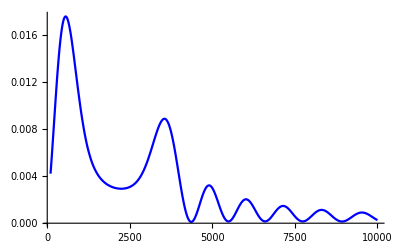

```mathematica
Plot[Abs[sgplus[0,q]^2*att/(lambda*q*p*be[q])],{q,100,10000},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}]
```

```mathematica
sg=-1
teta1=alfa+sg*teta
teta2=alfa-sg*teta
fam1=Sin[teta1]
fam2=Sin[teta2]
gam1=Cos[teta1]
gam2=Cos[teta2]
t1=t/gam1
t2=t/gam2
qpoly=p * rayon * gam2 / (2 * p + rayon * gam1) ;
att = Exp[-0.5*k*(t1+t2)* Im[chizero]];{"att",att}
s2max=0.25*t1*t2
u2max = u2 * s2max
gama=t2/t1
a=Sin[2*teta]*t1*0.5
kin=0.25*(t1-t2)*chizero/a
kinx=Re[kin]
kiny=Im[kin]
com=Sin[alfa]*(1+gam1*gam2*(1+rau))
kp3=0.5*k*(gama*a)^2
mu1=sg*(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta])
mu2=-sg * (Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta])
a1=sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta1]+ rau * Sin[alfa]Cos[teta1]) 
a2=-sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta2]+ rau * Sin[alfa]Cos[teta2])
acrist=-sg*h*com/rayon
acmax=acrist * s2max
g=gama * acrist * rayon/kp2
kap=u2max/acmax
pe=p*rayon/(gama^2*(rayon+p*mu2)-g*p)
qe[q_]:=q*rayon/(rayon-q*mu1-g * q);
be[q_]:=1/qe[q]+1/pe;
invle[q_]:=1/(pe+qe[q])+ g / rayon;
sgmoins[x_,q_]:=NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k * v^2 *invle[q]-k*v*kiny]*Cos[k*v*x/(q * p * be[q])], {v,-a,a}];
```

-1

-0.0815624

0.116469

-0.081472

0.116206

0.996676

0.993225

0.250834

0.251705

{att,0.791401}

0.0157841

68.2667+0.675283 ⅈ

1.00347

0.0246745

2.13988×10^-8-8.11064×10^-11 ⅈ

2.13988×10^-8

-8.11064×10^-11

0.0385315

31068.3

0.809323

1.19947

0.00975165

0.0150743

386.055

6.09352

0.197498

11.2032+0.11082 ⅈ

1852.26

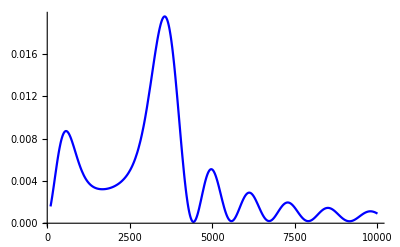

```mathematica
Plot[Abs[sgmoins[0,q]^2*att/(lambda*q*p*be[q])],{q,100,10000},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}]
```